### Defining model parameters and drug kinetics

```mathematica
λ= 2*10^6 ;d=2*0.05;β =5* 10^-10;c=10.0;a=0.5;u= 3 * 10^-5;k=1000;R=(λ β k)/(d a c) ;
Subscript[y, 0]=λ/a-(d * c)/(β k);
Subscript[x, 0]=λ/d;
```

```mathematica
R
```

2.

```mathematica
Drug[Cmax_,th_,T_,t_]:=Drug[Cmax,th,T,t]=Cmax 2^(-Mod[t,T]/th)
```

```mathematica
ϵ[Cmax_,th_,T_,t_,IC50_,M_,ρ_]:=1/(1+(Drug[Cmax,th,T,t]/(ρ IC50))^M)
```

Calculates the constant drug value corresponding to a time-averaged drug efficacy

```mathematica
timeavgeff[Cmax_,th_,T_,IC50_,M_,ρ_]:= NIntegrate[ϵ[Cmax,th,T,t,IC50,M,ρ]/T,{t,0,T}]
```

```mathematica
solefficacy[Cmax_,th_,T_,IC50_,M_,ρ_] :=Solve[1/(1+(drug/(ρ IC50))^M)==timeavgeff[Cmax,th,T,IC50,M,ρ],drug,Reals]
```

```mathematica
avgdrug[Cmax_,th_,T_,IC50_,M_,ρ_] :=drug/.solefficacy[Cmax,th,T,IC50,M,ρ][[1]]
```

### Deterministic dynamics of target cells and WT infected cells after the onset of therapy

#### Full 2 strain model of the target cells and the WT infected cells

```mathematica
solution[Cmax_,th_,T_,IC50_,M_]:=solution[Cmax,th,T,IC50,M] = NDSolve[{xf'[tt]==λ-d xf[tt]-(β k)/c(ϵ[Cmax,th,T,tt,IC50,M,1])xf[tt]yf[tt],yf'[tt]==(β k)/c(ϵ[Cmax,th,T,tt,IC50,M,1])xf[tt]yf[tt]-a yf[tt],xf[0]==Subscript[x, 0]/R,yf[0]==Subscript[y, 0]},{xf,yf},{tt,0,1000}]
```

```mathematica
xt[Cmax_,th_,T_,IC50_,M_,tt_]:= xf[tt]/.solution[Cmax,th,T,IC50,M][[1]];
```

```mathematica
yt[Cmax_,th_,T_,IC50_,M_,tt_]:= yf[tt]/.solution[Cmax,th,T,IC50,M][[1]];
```

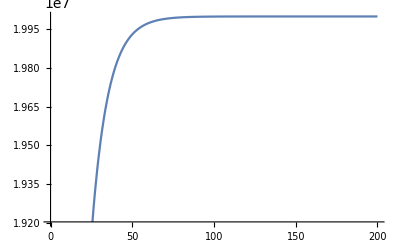

```mathematica
Plot[xt[20,1,1,10,10,t],{t,0,200}]
```

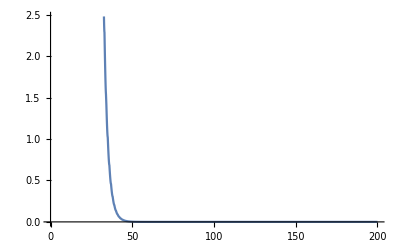

```mathematica
Plot[yt[20,1,1,10,10,t],{t,0,200}]
```

### Establishment probability of a pre-existing mutant

Calculated as a time-dependent birth-death process

```mathematica
Birth[s_,Cmaxw_,Cmaxr_,th_,T_,tp_,IC50_,M_,ρ_]:=Birth[s,Cmaxw,Cmaxr,th,T,tp,IC50,M,ρ]= Re[(1-s)* β*k/c*xt[Cmaxw,th,T,IC50,M,tp]*ϵ[Cmaxr,th,T,tp,IC50,M,ρ]]
```

```mathematica
rate[s_,Cmaxw_,Cmaxr_,th_,T_,t_,τ_?NumericQ,IC50_,M_,ρ_]:= rate[s,Cmaxw,Cmaxr,th,T,t,τ,IC50,M,ρ]=NIntegrate[a-Birth[s,Cmaxw,Cmaxr,th,T,tp,IC50,M,ρ],{tp,t,τ},Method->{"GaussKronrodRule","SymbolicProcessing"->0},WorkingPrecision->5]
```

```mathematica
pest[s_,Cmaxw_,Cmaxr_,th_,T_,t_?NumericQ,IC50_,M_,ρ_]:=
pest[s,Cmaxw,Cmaxr,th,T,t,IC50,M,ρ]= 1/(1+NIntegrate[Exp[rate[s,Cmaxw,Cmaxr,th,T,t,τ,IC50,M,ρ]],{τ,t,t+150},Method->{"GaussKronrodRule","SymbolicProcessing"->0},WorkingPrecision->5]*a)
```

#### Full resistance

Establishment probability corresponding to the drug at a constant value of Cmax

```mathematica
pest[0.3,20,20,Infinity,1,0,10,10,Infinity]
```

0.0788394

Establishment probability for the time-averaged drug efficacy

```mathematica
pest[0.3,avgdrug[20,1,1,10,10,1],20,Infinity,1,0,10,10,Infinity]
```

0.0759079

Establishment probability on varying the dosing period between T = 1 and T = 200 days

```mathematica
Table[pest[0.3,20,20,1*n,1*n,0,10,10,Infinity],{n,1,200,4}]
```

{0.0763611,0.0778073,0.0784671,0.0787021,0.0787763,0.0788023,0.0788136,0.0788197,0.0788234,0.078826,0.0788278,0.0788292,0.0788303,0.0788312,0.0788319,0.0788326,0.0788331,0.0788335,0.0788339,0.0788342,0.0788345,0.0788348,0.078835,0.0788353,0.0788355,0.0788356,0.0788358,0.0788359,0.0788361,0.0788362,0.0788363,0.0788364,0.0788365,0.0788366,0.0788367,0.0788368,0.0788369,0.078837,0.078837,0.0788371,0.0788371,0.0788372,0.0788373,0.0788373,0.0788374,0.0788374,0.0788375,0.0788375,0.0788375,0.0788376}

#### Partial resistance

Establishment probability corresponding to the drug at a constant value of Cmax

```mathematica
pest[0.3,20,20,Infinity,1,0,10,10,2]
```

8.81673×10^-12

Establishment probability for the time - averaged drug efficacy

```mathematica
pest[0.3,avgdrug[20,1,1,10,10,1],avgdrug[20,1,1,10,10,2],Infinity,1,0,10,10,2]
```

0.0418688

Establishment probability on varying the dosing period between T = 1 and T = 200 days

```mathematica
Table[pest[0.3,20,20,1*n,1*n,0,10,10,2],{n,1,200,4}]
```

{0.0413322,0.0405581,0.042372,0.0376228,0.0355329,0.0336372,0.0311372,0.0286397,0.0260607,0.02406,0.0214055,0.0194039,0.0176325,0.0160363,0.0146265,0.0133722,0.0122543,0.0112555,0.0103606,0.00955619,0.00883099,0.00817543,0.00758117,0.00704112,0.00654914,0.00609994,0.00568891,0.00531205,0.00496584,0.00464725,0.00435356,0.00408238,0.0038316,0.00359936,0.00338399,0.00318401,0.00299807,0.00282804,0.00266632,0.00251328,0.00237279,0.00224147,0.0021186,0.00200355,0.00189572,0.00179458,0.00169963,0.00161043,0.00152658,0.0014477}

### Risk of resistance due to rescue mutants

The risk is calculated by treating the process as a time-inhomogeneous Poisson process.

Correction term for setting the free pathogen population proportional to the infected cell population

```mathematica
m1[IC50_,M_, Cmaxw_]:=m1[IC50,M, Cmaxw]=ϵ[Cmaxw,Infinity,1,1,IC50,M,1](u Subscript[y, 0] a)/c;
```

Rate at which rescue mutants are produced

```mathematica
ν[s_,Cmaxw_,Cmaxr_,th_,T_,t_,IC50_,M_,ρ_]:=ν[s,Cmaxw,Cmaxr,th,T,t,IC50,M,ρ]=((β k)/c ϵ[Cmaxw,th,T,t,IC50,M,1]u)xt[Cmaxw,th,T,IC50,M,t]yt[Cmaxw,th,T,IC50,M,t]pest[s,Cmaxw,Cmaxr,th,T,t,IC50,M,ρ]
```

```mathematica
Subscript[Int, resc][s_,Cmaxw_,Cmaxr_,th_,T_,tfin_,IC50_,M_,ρ_]:=NIntegrate[1/d ν[s,Cmaxw,Cmaxr,th,T,t/d,IC50,M,ρ],{t,0,tfin},WorkingPrecision-> 4, Method->{"GaussKronrodRule","SymbolicProcessing"->0}]
```

Probability that at least one rescue mutant is produced

```mathematica
Subscript[P, resc][s_,Cmaxw_,Cmaxr_,th_,T_,tfin_,IC50_,M_,ρ_]:= 1 - Exp[-m1[IC50,M, Cmaxw]*pest[s,Cmaxw,Cmaxr,th,T,0,IC50,M,ρ]-Subscript[Int, resc][s,Cmaxw,Cmaxr,th,T,tfin,IC50,M,ρ] ]
```

#### Full resistance

Rescue probability corresponding to the drug at a constant value of Cmax

```mathematica
Subscript[P, resc][0.3,20,20,Infinity,1,10,10,10,Infinity]
```

0.00767237

Rescue probability corresponding to the drug at the constant time-averaged efficacy

```mathematica
Subscript[P, resc][0.3,avgdrug[20,1,1,10,10,1],20, Infinity,1,10,10,10,Infinity]
```

0.594452

Rescue probability on varying the drug dosing period from T = 1 to T  = 150

```mathematica
Table[Subscript[P, resc][0.3,20,20,1*n,1*n,10,10,10,Infinity],{n,1,21,4}]
```

{0.534913,0.390401,0.234608,0.12255,0.0640171,0.0377594}

```mathematica
Table[Subscript[P, resc][0.3,20,20,1*n,1*n,10,10,10,Infinity],{n,25,150,10}]
```

{0.0254223,0.0157143,0.0128326,0.0114729,0.0106793,0.0101603,0.00979244,0.00951898,0.00930773,0.00913966,0.00900473,0.00889144,0.00879589}

#### Partial resistance

Rescue probability corresponding to the drug at a constant value of Cmax

```mathematica
Subscript[P, resc][0.3,20,20,Infinity,1,10,10,10,2]
```

8.89511×10^-13

Rescue probability corresponding to the drug at the constant time-averaged efficacy

```mathematica
Subscript[P, resc][0.3,avgdrug[20,1,1,10,10,1],avgdrug[20,1,1,10,10,2], Infinity,1,10,10,10,2]
```

0.411358

Rescue probability on varying the drug dosing period from T = 1 to T  = 150

```mathematica
Table[Subscript[P, resc][0.3,20,20,1*n,1*n,10,10,10,2],{n,1,21,4}]
```

{0.361331,0.252177,0.147263,0.077971,0.0411583,0.0248338}

```mathematica
Table[Subscript[P, resc][0.3,20,20,1*n,1*n,10,10,10,2],{n,25,150,10}]
```

{0.0165869,0.0086729,0.00555822,0.00390709,0.0029017,0.00223625,0.00176727,0.0014248,0.00116627,0.000966238,0.000808534,0.000682203,0.000579667}